```mathematica
NS["fmri_schizo"]
```

```mathematica
(* definition of empirical covariance matrix, used a lot in the following *)covmatrix[data_]:=Block[{means=Mean@T@data,numindividuals=Length[data[[1]]]},
((data-means).T[data-means])/numindividuals]
```

```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\nanunana\\data_schizo"]
```

C:\Users\pglpm\repositories\nanunana\data_schizo

```mathematica
categories={"schizo","healthy"};
categoryfiles={"data_schizo.txt", "data_con.txt"};
numcategories=Length[categories];
quantities=Flatten@Import["data_params.txt","CSV"];
numquantities=Length@quantities;

Do[origsubjectfile[ii]=Import[categoryfiles[[ii]],"CSV"];numindividuals[ii]=Length[origsubjectfile[ii][[1]]],
{ii,numcategories}];
(* one row for each quantity, one column for each individual *)
minnumindividuals=Min@Table[numindividuals[ii],{ii,numcategories}];
```

```mathematica
minnumindividuals
```

20

```mathematica
numquantities
```

24

```mathematica
(* renormalize data for numerical stability *)

(* collect all data from all categories first *)
totaldata={};Do[totaldata=Join[totaldata,T[origsubjectfile[ii]]],{ii,numcategories}];
 (* individuals are in one column *)

tempmeans=Mean@totaldata;tempstds=Std@totaldata;
totaldata=(T@totaldata-tempmeans)/tempstds;

(* now renormalize and standardize *)
Do[origsubjectfile[ii]=(origsubjectfile[ii]-tempmeans)/tempstds,{ii,numcategories}]
```

```mathematica
(* a look at the eigenvectors and eigenvalues of the empirical covariance matrix *)
T@Eigensystem[covmatrix[totaldata]]//MF
```

(14.2147 | {-0.252106,0.253493,-0.253589,-0.252106,-0.252564,-0.247778,0.187105,0.242126,0.106396,-0.108138,-0.0816691,-0.246846,0.216833,-0.190525,-0.0000219514,0.21339,0.205562,0.238165,0.146126,0.233402,0.0406096,-0.196477,-0.183832,-0.239124}
6.24952 | {0.0881081,-0.0700235,0.0627457,0.0881081,0.0958721,0.1027,-0.251282,-0.140245,-0.294118,-0.35131,-0.362361,-0.109464,0.0924252,-0.142463,0.311795,0.199569,0.212661,0.00255998,-0.290613,-0.0951867,-0.322082,-0.228354,-0.243625,0.0023748}
1.39267 | {0.17027,-0.179077,0.183291,0.17027,0.151372,0.177724,0.0192478,-0.148825,0.345367,0.0238886,-0.0138442,-0.0125189,-0.0269176,-0.0458595,-0.352675,0.229364,0.251847,0.145241,0.0353099,-0.227895,0.420672,-0.264672,-0.291361,-0.172361}
1.0543 | {-0.0379193,-0.0567689,-0.034169,-0.0379193,-0.0171315,-0.0956853,0.157165,-0.0301345,-0.25147,0.103239,0.13119,0.05259,-0.434277,0.541862,0.087961,0.12651,0.0906208,0.348621,0.110608,-0.205485,-0.250492,-0.116433,-0.0727461,-0.303395}
0.410318 | {-0.0759956,0.111659,-0.123773,-0.0759956,-0.0274413,-0.0802521,-0.405403,-0.00744952,-0.231291,0.102145,0.190183,0.0131062,0.0543394,-0.00487602,-0.557519,0.0250992,-0.0203904,0.156297,-0.555777,0.0654469,-0.0302567,0.0119105,0.0809671,-0.169495}
0.317381 | {0.0515377,-0.0195953,0.0828254,0.0515377,0.0294976,0.0274664,-0.13521,0.0903787,0.227733,0.344317,0.371318,0.28405,0.395848,0.198757,0.457127,0.133718,0.119232,0.0672096,-0.229272,0.217179,-0.0199553,-0.127528,-0.108825,-0.0193583}
0.120734 | {-0.0380261,0.0895333,-0.0314499,-0.0380261,-0.0546763,-0.0502641,0.124767,0.144652,-0.150965,0.118057,0.0869979,0.216444,-0.155096,0.082418,-0.300337,0.172386,0.284781,-0.409128,0.0535296,0.116506,-0.168392,-0.19076,-0.339536,0.509146}
0.0836277 | {0.136565,-0.0470389,0.17575,0.136565,0.134472,0.157724,-0.0173427,0.243072,0.0540723,-0.222829,-0.170922,-0.315635,0.0965799,0.537136,-0.186947,-0.0401752,-0.113033,-0.0631501,0.0230183,0.534522,-0.0258373,-0.0685009,0.0196224,-0.0517674}
0.0627751 | {-0.0928696,0.112893,-0.131878,-0.0928696,-0.00369434,-0.113694,-0.172816,0.0489686,0.588581,-0.0981366,0.0561345,-0.283694,-0.494941,0.0820685,0.178738,-0.0149551,-0.048588,-0.157172,-0.353871,-0.0868462,-0.046673,-0.0758202,-0.0312895,0.122922}
0.0335756 | {0.0420965,0.0830106,-0.00133933,0.0420965,0.0701338,0.0658177,-0.297284,-0.00760144,0.00032777,-0.0512086,-0.0799038,0.434744,-0.471451,-0.283035,0.0802546,-0.0628953,-0.0371194,0.0965907,0.190567,0.519908,0.0746677,-0.0612115,-0.0978552,-0.211826}
0.024925 | {-0.112716,-0.00459119,-0.133218,-0.112716,-0.0738909,-0.201491,-0.100278,-0.0770756,-0.118141,-0.208242,-0.295555,0.250803,0.00100597,0.361406,0.141457,0.113583,0.177534,0.0868078,-0.129916,0.00982007,0.602587,0.174383,0.101602,0.252568}
0.018458 | {-0.0972353,-0.0784629,-0.146318,-0.0972353,-0.169019,-0.1382,0.00380298,-0.19998,0.102688,-0.0367822,-0.215196,0.271613,0.202487,0.198052,-0.0724869,-0.397752,-0.38963,-0.208878,-0.0295626,-0.10876,-0.0233602,-0.286804,-0.396358,-0.20528}
0.00955287 | {0.00732451,-0.0982947,-0.0203678,0.00732451,-0.0269188,-0.0837488,0.0442531,-0.0506202,0.454144,-0.222989,-0.213816,0.412394,0.13632,0.050341,-0.245578,0.149264,0.108809,0.235752,0.0357749,-0.0158815,-0.485254,0.170717,0.245551,0.0907361}
0.00317449 | {0.157164,0.156619,0.185568,0.157164,0.0550272,-0.0688269,0.415246,0.356277,-0.023673,0.114544,-0.236555,0.105681,-0.0978276,-0.12541,0.0158356,-0.306455,-0.0446535,0.359241,-0.410555,-0.0191103,0.0309047,0.112232,-0.233893,0.126527}
0.00214685 | {0.0677446,-0.00312528,0.0281134,0.0677446,-0.303472,-0.032602,-0.345728,-0.234859,0.082392,0.396537,-0.21928,-0.278707,0.0127651,0.0835791,-0.022886,-0.224068,0.242634,0.186425,0.200047,0.076497,-0.113415,0.344475,-0.287302,0.144715}
0.00102226 | {-0.0300548,-0.0538846,-0.0771565,-0.0300548,0.0298121,0.0420793,-0.01589,-0.26488,-0.0308108,-0.0573935,0.163451,-0.114105,0.0153963,-0.0446133,-0.0144096,-0.00330003,-0.351699,0.51535,0.089958,0.123477,0.0106715,-0.388379,0.00929974,0.553338}
0.00059228 | {0.0759229,0.299383,0.127439,0.0759229,-0.0322301,-0.0341263,-0.481579,0.54461,0.00125795,-0.052494,-0.0453135,0.0897931,0.0801058,0.0692856,-0.0100435,-0.00673672,-0.141337,0.092416,0.307522,-0.413744,0.0207686,-0.154189,0.020952,0.09341}
0.000212162 | {-0.0505695,0.401926,-0.258572,-0.0505695,0.59288,0.094908,-0.00270402,-0.152001,0.031502,-0.239085,0.222698,0.010751,0.133219,0.102831,-0.0134945,-0.26935,0.191463,0.0735032,0.120026,-0.058064,-0.0372129,0.226512,-0.247508,0.0121503}
0.000185903 | {-0.100126,-0.642078,0.113026,-0.100126,0.16445,-0.41466,-0.141189,0.264472,-0.0359906,-0.232342,0.265611,-0.0534869,0.000367028,-0.110099,-0.00999987,-0.129445,0.0329458,0.0646544,0.065713,0.0197409,-0.00169148,0.185064,-0.249805,0.0418266}
0.0000712043 | {0.198988,0.0599773,-0.120309,0.198988,0.454375,-0.641533,-0.0169828,-0.10912,-0.00681014,0.334494,-0.246098,-0.087657,0.0324256,-0.0336667,-0.0073424,0.140309,-0.0759473,-0.0964677,0.0727079,0.0537472,-0.0218667,-0.153223,0.150493,-0.0236655}
0.0000504526 | {-0.0706204,-0.324703,-0.593815,-0.0706204,0.222988,0.391089,-0.0354147,0.303133,0.00823545,0.290199,-0.253267,0.0000555223,-0.00835054,-0.0122723,0.00897805,0.182639,-0.164488,0.045162,-0.00495158,-0.0465412,-0.00869708,0.112441,-0.0952795,0.0314642}
0.0000199611 | {-0.442902,0.103414,0.528552,-0.442902,0.290489,0.0610774,-0.0285206,-0.0763055,0.0252988,0.205439,-0.207334,-0.000106371,0.000605271,0.00771809,-0.0157214,0.237378,-0.221055,0.00853473,0.00122915,-0.000508022,-0.0339296,0.127814,-0.117868,0.00737828}
6.25293×10^-6 | {0.218691,0.162435,-0.04958,0.218691,-0.158961,-0.104004,0.0397396,-0.0891254,-0.00825308,-0.168887,0.155647,0.00391181,0.00390785,0.00949551,0.00386447,0.505708,-0.457709,-0.0246401,-0.00395142,0.00882115,0.0150842,0.415892,-0.370504,-0.0232124}
1.5259×10^-16 | {0.707107,9.9811×10^-10,7.08011×10^-9,-0.707107,2.10899×10^-9,-9.67184×10^-13,-2.02096×10^-10,-8.87363×10^-10,3.76963×10^-10,3.47561×10^-9,-3.36096×10^-9,-9.16711×10^-11,-2.34929×10^-10,-6.96202×10^-11,-2.0299×10^-10,1.03973×10^-9,-7.68589×10^-10,-5.48382×10^-11,-3.68831×10^-10,1.92693×10^-10,-5.43458×10^-10,-2.44743×10^-10,3.62052×10^-10,4.36382×10^-11})

```mathematica
eigenvectors=T[Eigenvectors[covmatrix[totaldata]]];
ieigenvectors=Inverse[eigenvectors];

Do[origsubjectfile[ii]=ieigenvectors.origsubjectfile[ii],{ii,numcategories}];
```

```mathematica
(* we can use at most (num.subjects -2) quantities. We choose those that have the covariance matrix with largest volume *)

(* this selects all possible subsets of (num.subjs-2) quantities out of all available quantities *)
(*numusedquantities=minnumindividuals-2;*)
numusedquantities=minnumindividuals-7;

trialquantities=Subsets[Range[numquantities],{numusedquantities}];
totcovmatrix=covmatrix[totaldata];

(* this calculates all determinants of cov. matrices for these subsets *)
trialdeterminants=Table[Det[totcovmatrix[[ii,ii]]],{ii,trialquantities}];

(* this is the subset with largest scatter *)
bestquantities=Ordering[Abs[trialdeterminants],-1][[1]];
chosenquantities=trialquantities[[bestquantities]];

quantities[[chosenquantities]]
```

{ normalized weighted degree2, closeness centrality2, graphweights3, shortest path3, cluster coeff.3, normalized weighted degree3, closeness centrality3, graphweights4, shortest path4, cluster coeff.4, weighted degree4, normalized weighted degree4, closeness centrality4}

```mathematica
(* select subsets of data, for each category, corresponding to the optimal quantities *)
quantities=quantities[[chosenquantities]];numquantities=Length@quantities;
Do[subjectfile[ii]=origsubjectfile[ii][[chosenquantities]],{ii,numcategories}];
```

```mathematica
Do[means[ii]=Mean@T@subjectfile[ii];
tparameter[ii]=numindividuals[ii]+1-numquantities;
tcovariance[ii]=covmatrix[ subjectfile[ii]];
,{ii,numcategories}];
```

```mathematica
Det@tcovariance[1]
```

1.30073×10^-16

```mathematica
(* second best *)quantities[[trialquantities[[Ordering[Abs[trialdeterminants],-2][[1]]]]]]
```

{ graphweights2, shortest path2}⟦{2,21}⟧

```mathematica
Det[totcovmatrix[[trialquantities[[bestquantities]],trialquantities[[bestquantities]]]]]
```

3.8405×10^-9

```mathematica
(* this is the principal component analysis: eigenvalues and eigenvectors *)(pcomp=T@Eigensystem[covmatrix[PrincipalComponents[T@totaldata]]])//MF
```

(16.9858 | {0.231435,-0.0330681,-0.368568,0.201248,0.209054,-0.27621,0.0894835,0.0955094,-0.223842,-0.12113,0.0842881,0.207647,-0.0304622,-0.00772911,0.177022,0.253152,-0.165435,-0.0924595,0.281637,0.00750198,-0.0754809,-0.307577,-0.0609457,0.19102,-0.387277,0.121185}
3.84988 | {-0.00861187,-0.127002,0.142351,0.000349231,-0.100862,0.085564,0.0230135,0.533283,0.245201,0.146278,-0.0388464,-0.0182166,-0.0830141,-0.26233,-0.0888818,0.00893267,0.0600858,0.0151159,-0.0290918,0.105174,-0.280422,-0.604922,0.0315232,0.0366688,0.173779,0.0348804}
1.7061 | {0.136175,-0.201318,0.358985,0.207293,0.1004,0.00587044,-0.0780877,-0.491876,0.340193,-0.222482,-0.0394085,0.0689162,-0.0530246,-0.2057,0.0694632,0.150935,-0.0175484,-0.296265,0.313223,0.057732,-0.194851,-0.0370587,-0.061984,-0.0153219,0.171488,-0.0657503}
1.30521 | {0.0385872,-0.150138,0.0283515,0.0833949,0.0235513,-0.233348,-0.127667,0.601367,0.0556878,-0.198137,-0.0738724,0.0294668,-0.0594766,-0.0229117,-0.0275191,0.0201448,-0.184461,-0.306375,0.0772354,0.0121863,-0.00558471,0.532823,-0.152956,0.002347,0.158867,-0.121563}
0.520708 | {0.074727,-0.0228481,0.230395,-0.128633,-0.00525349,0.410213,0.0676276,0.079089,-0.362238,0.0213432,-0.151046,0.135809,-0.233991,-0.189055,-0.0277391,0.239718,0.124792,0.202513,0.171773,-0.438478,-0.210407,0.177582,-0.187007,0.156673,-0.0852424,-0.0503177}
0.235453 | {0.121532,0.0322805,-0.0247815,-0.189795,0.205972,-0.379847,0.104918,-0.109211,-0.0992115,0.00294883,-0.00900134,-0.124354,-0.120586,0.061559,0.0594018,0.0584852,-0.229399,0.404817,-0.0127474,-0.0458536,-0.13692,-0.0427083,-0.275475,-0.020061,0.579807,0.18823}
0.131208 | {0.0222636,-0.175071,-0.528439,0.17194,-0.230376,0.144109,0.0186071,-0.124887,0.0659119,0.270107,-0.104898,-0.120559,-0.134057,-0.299821,-0.109444,0.0641271,-0.062902,0.143168,0.163137,0.231174,-0.230153,0.317281,0.223103,0.0277564,0.101461,0.156459}
0.0821626 | {0.18633,0.00784758,-0.0175359,0.0453116,0.0223208,0.0839523,-0.564477,0.00778144,-0.432549,0.200808,0.0402812,-0.0855401,-0.000432486,0.0186416,-0.0636851,0.104679,-0.00662728,-0.191935,0.204252,-0.0391392,0.279826,-0.191118,0.234334,-0.113181,0.342049,-0.0721936}
0.0556378 | {-0.0847985,0.135789,-0.196275,0.111039,-0.162292,0.084337,-0.0852208,0.075308,0.324561,-0.180558,-0.302205,-0.105324,-0.00985,0.231834,-0.0795842,0.0887072,-0.0208543,0.349671,0.451511,-0.103611,0.262285,-0.142194,-0.192913,-0.138414,-0.0181965,-0.292752}
0.0169137 | {0.0250435,-0.110146,-0.214287,-0.41592,0.140409,0.223899,0.0725608,0.0774453,0.241066,-0.303859,0.00524574,-0.0526665,-0.152368,0.0428115,0.26738,0.134251,-0.0817585,-0.139236,-0.00420858,-0.300765,0.0825268,-0.0196888,0.404764,-0.24723,0.0675306,0.257199}
0.0128422 | {-0.114721,0.168197,-0.244201,0.22966,0.335304,0.381287,-0.0576613,0.0395888,-0.128252,-0.291842,0.0429167,0.180604,0.307597,-0.218101,0.177878,-0.268893,-0.121188,0.098522,-0.120901,0.0453308,-0.20446,-0.0324518,-0.0643383,-0.12959,0.214351,-0.224635}
0.00535168 | {-0.0140843,-0.300188,0.0416341,0.105001,-0.0970404,0.0956285,-0.165893,-0.0274869,0.118081,-0.199627,0.176477,-0.0304668,0.297714,-0.200698,-0.242523,0.0613534,-0.33482,0.21194,-0.168045,-0.238299,0.32673,-0.0320802,-0.0225504,0.412831,-0.00153535,0.227946}
0.00447836 | {-0.0229738,-0.0513742,-0.150565,0.106776,-0.0591763,0.221116,0.111617,-0.0816073,-0.0790853,-0.17917,-0.364237,0.108615,-0.267311,0.395667,-0.0337889,0.0863256,0.0187259,-0.229125,-0.30278,0.168215,0.0489298,-0.115833,-0.0142576,0.4578,0.267913,-0.0404172}
0.00289297 | {-0.23285,0.151289,0.210321,0.0467373,-0.118824,-0.0954408,-0.330944,0.0317991,-0.0269729,-0.0986462,-0.0144338,-0.292131,-0.0959331,0.0922909,0.476048,-0.041001,-0.185906,0.204387,0.050654,0.0387763,-0.280546,0.040139,0.317612,0.345618,-0.120392,-0.0716509}
0.000917666 | {-0.408556,-0.158053,-0.233134,-0.00825181,0.172047,-0.0730215,-0.11087,-0.0288503,0.141272,0.211824,0.232202,-0.0131815,-0.215059,-0.208103,0.339008,0.0184965,0.36988,-0.0773557,-0.00245291,-0.138055,0.258068,-0.00496199,-0.283337,0.220247,0.111023,-0.110824}
0.000565879 | {0.0554757,0.100931,0.00604522,0.141969,-0.543753,0.14621,0.0190662,0.0383225,-0.169866,-0.266568,0.176376,-0.184122,0.0588409,-0.0321537,0.320977,0.113154,0.140164,-0.100156,-0.0351756,0.128558,0.0439797,-0.0275739,-0.366441,-0.201027,0.0731102,0.363656}
0.000281803 | {0.00212702,0.353858,-0.0481764,-0.267787,-0.00771839,-0.126591,-0.31287,-0.0301683,0.116957,-0.138295,-0.136397,0.250588,0.0280383,-0.309491,-0.0625919,0.526802,0.0998569,0.106421,-0.288328,0.277426,0.0436837,0.0542139,-0.00240056,-0.00801513,-0.0618778,-0.0592643}
0.000128046 | {-0.180767,0.243812,-0.0849001,-0.186349,-0.30111,-0.188755,0.264712,-0.0268529,-0.120843,-0.293026,0.327531,0.135882,0.0621792,-0.109972,-0.244858,-0.061893,0.14914,-0.103809,0.302017,-0.0826154,-0.0581158,-0.0252852,0.256033,0.242851,0.26575,-0.180757}
0.0000899332 | {-0.103604,-0.0621881,0.0979284,0.501528,-0.037357,-0.206684,-0.0553881,0.0191722,-0.0526244,-0.208699,0.0688537,0.301807,-0.432712,-0.00815627,-0.0899351,-0.044742,0.173789,0.278636,-0.19278,-0.153682,0.0760164,0.00183144,0.267579,-0.277827,0.0232737,0.115964}
0.0000398096 | {0.491031,-0.191877,-0.0907158,-0.264233,-0.0607497,0.115493,-0.272236,-0.000503202,0.10903,-0.178964,0.348503,0.123345,-0.254387,0.122659,-0.00818782,-0.324505,0.160994,0.218765,0.00150413,0.225161,-0.0576,0.0331985,-0.103835,0.112568,-0.0922763,-0.162183}
9.23608×10^-6 | {0.0753794,-0.195699,0.176748,-0.0961002,0.0151403,-0.0315005,0.340949,0.0210929,-0.240752,-0.133551,-0.226032,-0.105557,-0.111097,-0.388828,0.220767,-0.119,-0.0787996,0.138726,0.0601666,0.353016,0.465194,-0.0321325,0.13749,-0.00915072,-0.0313605,-0.205109}
3.75922×10^-6 | {0.336323,0.129194,-0.0917176,0.140789,0.195445,-0.164098,-0.0213918,0.0362242,0.0299251,-0.211528,-0.264228,-0.457046,0.15479,-0.163315,-0.0869323,-0.128832,0.530656,-0.0125934,-0.0852278,-0.197552,-0.0338333,0.0280941,0.0858485,0.172673,-0.0142156,0.0925489}
3.69413×10^-7 | {-0.123191,0.283915,0.0502516,-0.131338,0.0505247,0.0110259,-0.195969,-0.00548397,0.0380788,0.00166268,-0.289739,0.280295,-0.135174,-0.143882,-0.0480216,-0.477974,-0.0467131,-0.0896131,0.270811,0.0654691,0.124403,-0.00236736,-0.103945,0.126016,-0.0365685,0.527528}
-6.6748×10^-16 | {0.397157,0.206509,0.0835846,0.166207,-0.134087,0.0218808,0.166702,0.100099,0.246136,0.319422,-0.00300022,0.375974,0.232898,0.055281,0.400965,0.0232076,0.0648767,0.102455,0.0191577,-0.127788,0.17478,0.129252,0.175278,0.17034,0.218537,0.}
4.62153×10^-16 | {-0.175417,-0.116069,0.178548,0.0448532,0.352575,0.182959,0.0589788,0.16715,-0.0242764,-0.0668772,0.166234,0.00982815,0.198043,0.270217,-0.0699743,0.239867,0.31503,0.218864,0.281279,0.404745,0.0451737,0.139908,0.120663,0.0820516,0.0727709,0.294816}
2.30442×10^-16 | {0.133565,0.510591,0.0739902,0.196883,0.2227,0.23525,0.158042,0.0579208,0.156136,0.0636712,0.349336,-0.298223,-0.396223,-0.0897297,-0.156682,0.0806434,-0.235444,-0.0857968,-0.0178066,0.06672,0.172006,0.0484362,-0.0295485,0.0866692,-0.0238193,0.})

```mathematica
(* the volume of the cov. matrix from the (num.subjs -2) most relevant quantities principal components *)
Apply[Times,pcomp[[1;;11,1]]]
```

2.32594×10^-6

```mathematica
(* we show the two distributions in a 2D section of the (numquantities)-dimensional space. This section is chosen this way:
1. the centroids of the two distributions have coords (1,0) and (-1,0);
2. point of max overlap of the distributions, intended as Log[p1*p2] (where they must be equal) has coords (0,1).

This section is represented by a (numquantities x 3)-dimensional matrix; it has 3 columns because it's an affine transformation *)
```

```mathematica
(* overlap function Log[p1*p2] *)
vector=Array[x,numquantities];
overlap[vector_]:=Sum[Log@PDF[MultivariateTDistribution[means[ii],tcovariance[ii],tparameter[ii]],vector],{ii,numcategories}];
```

```mathematica
(* find the maximum *)findmax=Maximize[overlap[vector],vector,Reals]
```

{-3.71886,{x[1]→0.111303,x[2]→0.140505}}

```mathematica
maximum=vector/.findmax[[2]]
```

{0.111303,0.140505}

```mathematica
(* matrix of the target vectors in the 3D section *)
targetvectors={{1,-1,0},{0,0,1},{1,1,1}};

(* matrix of the vectors to appear in the 3D section *)
originalvectors = T@{means[1],means[2],maximum};

(* section matrix *)
sectionmatrix=originalvectors.Inverse[targetvectors];
```

```mathematica
(* define the distribution in the 2D section *)Do[distribution[ii,x_,y_]=PDF[MultivariateTDistribution[means[ii],tcovariance[ii],tparameter[ii]],FS[sectionmatrix.{x,y,1}]],{ii,numcategories}];
```

```mathematica
rangex=5;rangey=5;Plot3D[{distribution[1,x,y],distribution[2,x,y]},{x,-rangex,rangex},{y,-rangey,rangey},AxesLabel->{x,y,P},PlotRange->All,PlotStyle->{{red,Opacity[0.75]},{blue,Opacity[0.75]}},PlotPoints->75,Mesh->None,BoxRatios->{1,1,1/GoldenRatio},PlotLegends->mylegends[categories],ViewPoint->Dynamic[viewpoint]]
```

-Graphics3D-

```mathematica
(* we plot a 3D section the 1-std ellipsoids of the distributions in the (numquantities)-dimensional space. This section is chosen this way:
1. the centroids of the two distributions have coords (1,0,0) and (-1,0,0);
2. the largest eigenvector of the ellipsoid of the 1st distribution has coords (0,1,0);
3. the largest eigenvector of the ellipsoid of the 2nd distribution has coords (0,0,1);
- other choices are possible, of course *)
(* This section is represented by a (numquantities x 4)-dimensional matrix; it has four columns because it's an affine transformation *)
```

```mathematica
tparameter[1]
```

3

```mathematica
numindividuals[1]
```

13

```mathematica
numquantities
```

11

```mathematica
(* find the largest eigenvectors of the two distributions *)
Do[largestvector[ii]=Eigensystem[tcovariance[ii]][[2,1]],{ii,numcategories}];

(* matrix of the target vectors in the 3D section *)
targetvectors={{1,-1,0,0},{0,0,1,0},{0,0,0,1},{1,1,1,1}};

(* matrix of the vectors to appear in the 3D section *)
originalvectors = T@{means[1],means[2],largestvector[1],largestvector[2]};

(* section matrix *)
sectionmatrix=originalvectors.Inverse[targetvectors];

(* the probability level of a multinomial t-distribution is given by the inverse of the FRatioDistribution *)
plevel[ii_,p_]:=InverseCDF[FRatioDistribution[numquantities,tparameter[ii]],p];
```

```mathematica
(* to map a generic 3D point of coordinates (x,y,z) to the (numquantities)-dimensional space we multiply
sectionmatrix.{x,y,z,1} *)
mappoint[x_,y_,z_]=sectionmatrix.{x,y,z,1};
```

```mathematica
Do[mapellipse[ii,x_,y_,z_]=FS[((sectionmatrix.{x,y,z,1})-means[ii]).Inverse[tcovariance[ii]].((sectionmatrix.{x,y,z,1})-means[ii])],{ii,numcategories}];
```

```mathematica
mapellipse[2,x,y,z]
```

6.77712+6.77712 x^2+0.422528 y^2+x (13.5542-1.74665 y-0.00259437 z)+y (-1.74665+0.0628795 z)+(-0.00259437+0.0334821 z) z

```mathematica
colours={blue,red,yellow};Do[cont[i]=ContourPlot3D[mapellipse[i,x,y,z],{x,-50,50},{y,-50,50},{z,-70,70},Contours->{(*plevel[i,0.5]*numquantities,*)plevel[i,0.5]*numquantities},ContourStyle->{Directive[Opacity[0.75],Thick,colours[[i]]],Directive[Dashed,Opacity[0.75],Thick,colours[[i]]]},PlotPoints->50,AspectRatio->Auto,Mesh->None,PlotLegends->If[i==3,mylegendsc[{(*blue,red,yellow,White,*){Gray,Thick},{Gray,Dashed,Thick}},{(*"H","A","MCI"," ", *)"50% region surface","95% region surface"}],None],(*PlotLabel->mylabels[{"1 and 2 standard deviations"}],*)PlotRange->All],{i,numcategories}];
centres=Graphics[{{blue,PointSize[Large],Point[{0,0}]},{red,PointSize[Large],Point[{1/2,Sqrt[3]/2}]},{yellow,PointSize[Large],Point[{1,0}]}}];texts=Graphics[{Text[Style["HEALTHY",blue,18,Thickness[1/50],FontFamily->"Palatino"],{0,-0.1},{0.8,0},{1,-0.1}],Text[Style["ALZHEIMER",red,18,Thickness[1/50],FontFamily->"Palatino"],{1/2+0.5,Sqrt[3]/2},{0,0},{0.07,-1}],Text[Style["MCI",yellow,15,Thickness[1/50],FontFamily->"Palatino"],{1+0.5,0},{0.5,0},{0.6,1}]}];
```

```mathematica
show[{cont[1],cont[2]}]
```

```mathematica
Do[distribution[ii,x_,y_,z_]=PDF[MultivariateTDistribution[means[ii],tcovariance[ii],tparameter[ii]],FS[sectionmatrix.{x,y,z,1}]],{ii,numcategories}];
```

```mathematica
vector=Array[x,numquantities];

posdefmatrix=uppersymmetrize@Array[y,{numquantities,numquantities}];posdefmatrix=posdefmatrix-DiagonalMatrix@Diagonal@posdefmatrix/2;

variables=Join[vector,Diagonal@posdefmatrix,abovediag@posdefmatrix];

Do[cvm=covmatrix[subjectfile[ii]];nn=numindividuals[ii];me=means[ii];
normconstant=Pi^((numquantities^2-numquantities)/4)*Product[Gamma[(nn+1-ii)/2],{ii,numquantities}];

(*density[ii]=Piecewise[{{(nn/2)^(numquantities*(nn+1)/2)/normconstant /Pi^(numquantities/2)*Det[cvm]^(nn/2)/
Det[posdefmatrix]^(numquantities/2+nn/2+1)*
Exp[-Tr[(nn*cvm).Inverse[posdefmatrix]]/2]*
Exp[-nn*((vector-me).Inverse[posdefmatrix].(vector-me))/2],Det[posdefmatrix]>0}}];


pdf[ii]=ProbabilityDistribution[density[ii],Replace[Table[{variables[[jj]],-Infinity,+Infinity},{jj,Length[variables]}],List->Sequence,1,Heads->True]];*)

pdf[ii]=ParameterMixtureDistribution[
MultinormalDistribution[me,Inverse[matr]],{matr\[Distributed]InverseWishartMatrixDistribution[tparameter[ii],cvm]}];

,{ii,numcategories}];
```

```mathematica
{subjectfile[1]//T//
MF,subjectfile[2]//T//
MF}
```

{(-0.72729 | 1.00526
0.141599 | -0.860681
0.469422 | -0.80499
-0.90231 | 1.41165
-0.893063 | 0.559066
1.37082 | -0.767929
0.685563 | 0.268201
1.38714 | 1.01555
0.529619 | 0.392873
1.63288 | -0.545627
-0.0581967 | 0.0758309
-0.463218 | 0.930503
-0.19023 | -0.446463),(-0.898049 | -1.10463
-0.674262 | 0.629727
-0.558459 | 1.31557
0.938987 | -0.555799
1.69524 | -0.935009
-1.2135 | 1.68217
0.0552334 | 0.504265
-0.984788 | -1.36734
-2.78033 | -2.44444
0.469279 | -0.162447
0.054722 | 1.02032
0.468498 | -1.18878
0.444684 | 0.373158)}

```mathematica
subjectfilefake[2]=N@T@Join[Table[{1,10},{20}],Table[{10,1},{20}],Table[{10,10},{10}]];
```

```mathematica
subjectfilefake[1]=-subjectfilefake[2];
```

```mathematica
subjectfilefake[2]=N@T@Table[{RandomInteger[{0,10}],RandomInteger[{1,10}]},{50}]
```

{{2.,0.,7.,5.,0.,5.,4.,6.,9.,2.,2.,3.,3.,9.,4.,4.,4.,8.,0.,2.,7.,9.,2.,6.,6.,10.,1.,8.,3.,3.,6.,9.,1.,3.,9.,10.,2.,7.,0.,8.,7.,8.,2.,5.,1.,8.,7.,1.,6.,4.},{3.,1.,9.,8.,8.,10.,1.,9.,9.,2.,9.,1.,2.,8.,5.,1.,7.,1.,7.,6.,8.,5.,2.,8.,4.,6.,9.,4.,6.,8.,3.,3.,1.,2.,4.,9.,2.,8.,7.,7.,5.,7.,3.,5.,8.,4.,10.,10.,7.,4.}}

```mathematica
{subjectfilefake[1]//T//MF,subjectfilefake[2]//T//MF}
```

{(-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.),(1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.)}

```mathematica
{Mean@T@subjectfilefake[1],Mean@T@subjectfilefake[2]}
```

{{-5.5,-6.},{5.5,6.}}

```mathematica
covmatrix[subjectfilefake[2]]//T//MF
```

(8.9824 | 1.4648
1.4648 | 8.3696)

```mathematica
Eigenvalues[covmatrix[subjectfilefake[2]]]
```

{32.4,6.48}

```mathematica
means[1]
```

{-0.138987,0.235658,0.0709035,0.0213909,0.0812277,-0.0268703,-0.0899908,0.0505261,0.198721,0.134221,0.205749}

```mathematica
Length@subjectfile[1][[3]]
```

13

```mathematica
subjectfile[1]//MF
```

(-1.26009 | 0.501559 | 1.1314 | -1.11038 | -1.07815 | 1.20089 | -0.398 | -0.600063 | 0.512067 | 0.620988 | -0.442887 | -1.1059 | 0.221734
0.0043185 | -0.566129 | -0.0393711 | -0.00103826 | -0.458223 | -0.347146 | -0.130624 | 4.62607 | 0.00364653 | 0.542645 | -0.237098 | 0.0760029 | -0.409491
-1.2019 | 0.0322257 | 1.72134 | -0.738341 | -1.30925 | 1.70794 | -0.641672 | -0.0828977 | 1.45952 | 1.06903 | -0.299447 | -1.04597 | 0.251174
1.29357 | -0.649743 | -1.71127 | 0.910856 | 0.855945 | -1.53064 | 0.535988 | 1.09592 | -0.886338 | -0.570233 | 0.37646 | 1.04124 | -0.483672
-1.58527 | 0.421639 | 1.35495 | -0.874144 | -1.13503 | 1.19867 | 0.18084 | -0.395401 | 1.91054 | 0.532606 | -0.19324 | -0.976263 | 0.616074
0.430863 | 0.612228 | -1.30025 | 0.231122 | 0.590838 | 0.277314 | 0.414253 | -0.0204708 | -2.42383 | -0.537831 | 0.211235 | 1.13804 | 0.0271871
0.824478 | 0.219653 | -2.91348 | 0.748841 | 0.791498 | -1.27554 | 0.440945 | 0.610519 | -1.74127 | -0.227677 | 0.510956 | 0.754564 | 0.0866335
0.65822 | 0.346196 | -2.10177 | 0.641923 | 0.629982 | -1.18436 | 0.361536 | 0.52737 | -0.814603 | 0.0226257 | 0.645179 | 0.600399 | 0.324138
-0.114825 | -0.167323 | 0.778098 | -0.776619 | -0.748899 | 1.61866 | 0.351106 | 1.53419 | 0.228286 | 1.33364 | -0.438889 | -0.288752 | -0.725315
1.21029 | -1.01206 | -0.59573 | 1.57706 | 0.555342 | -0.682318 | 0.175177 | 0.520006 | 0.609721 | -0.862899 | -0.196065 | 0.990186 | -0.543831
-0.311152 | -0.47372 | 0.195917 | -0.319279 | -0.456651 | -0.359521 | -0.258373 | 4.62066 | 0.837971 | 0.118938 | -0.339612 | -0.254446 | -0.325986)

```mathematica
means[1]
```

{0.235658,0.0709035,0.0213909,0.0812277,-0.0268703,0.0505261,0.198721,0.134221,0.205749,0.110778}

```mathematica
datax=Table[RandomVariate[NormalDistribution[0,1]],{ii,numquantities}];
```

```mathematica
datax=Table[RandomVariate[NormalDistribution[means[1][[ii]],2*Std[subjectfile[1][[ii]]]]],{ii,numquantities}];
```

```mathematica
datax
```

{0.577807,0.527777,0.991599,-0.68966,-0.370756,1.56901,-0.390612,-1.09595,0.422303,-1.04054}

```mathematica
numquantities
```

18

```mathematica
minnumindividuals
```

20

```mathematica
subjectfile[1]//T//MF
```

(-0.874477 | 1.65365 | 1.44691 | 2.65826 | 0.0684616 | 0.059963 | -0.841333 | 2.03694 | -1.37325 | 1.20044 | 0.476965 | 0.550985 | 1.92886 | 1.7093 | 1.83715 | -0.468472 | -0.472102 | -0.665509
2.25727 | -2.0744 | -1.94357 | -0.873166 | -0.707365 | -0.954733 | 0.826926 | -0.418342 | -0.169224 | 0.47386 | -0.156681 | -1.64586 | -1.82777 | -1.59247 | -0.539308 | -0.0372756 | -0.209757 | 1.46805
-1.0234 | 1.12197 | 0.85237 | -0.0186718 | -1.16096 | -1.19206 | -1.30568 | 1.59871 | -1.73623 | 0.60164 | 0.984486 | 0.700248 | 1.12615 | 0.689373 | -0.344339 | -0.931105 | -0.964714 | -0.774881
0.0197358 | 0.265623 | -0.0768745 | -0.670828 | -0.359003 | -0.373649 | -0.0649994 | -0.71574 | 0.777608 | 0.468056 | 0.968283 | 0.895464 | 0.293878 | -0.352123 | -0.520281 | -0.649118 | -0.661533 | -0.478427
0.296885 | -0.0288257 | -0.205178 | -0.410294 | 1.2817 | 1.27235 | 1.15864 | -0.856138 | 1.43088 | 0.218426 | -0.805864 | -0.270658 | 0.0991769 | -0.20748 | -0.41182 | 0.702722 | 0.738603 | 0.232227
0.0646406 | 0.533517 | -0.0453817 | 0.514468 | 0.242093 | 0.278951 | 0.0384234 | -1.35741 | 1.00575 | -0.788984 | -0.0834256 | 0.195293 | 0.68078 | -0.408173 | 0.215783 | -0.274576 | -0.240145 | -0.393613
-1.21082 | -0.0605758 | 0.967864 | -0.295466 | -0.983384 | -0.732413 | -1.17836 | 0.909527 | -1.08603 | 0.272713 | 0.914828 | 0.741957 | -0.396217 | 1.2098 | -0.405836 | -0.885523 | -0.834586 | -0.758127
-0.696474 | 0.566023 | 0.368661 | -0.644262 | -1.2524 | -1.26608 | -1.23712 | 0.417523 | -0.602647 | 0.396597 | 1.09817 | 0.790357 | 0.367748 | 0.0401915 | -0.507753 | -0.950077 | -0.980779 | -0.770715
-1.5166 | -0.0019498 | 0.839282 | -0.668494 | -1.91473 | -1.89337 | -1.71229 | 1.49092 | -2.47769 | 0.393136 | 1.12263 | 0.761607 | -0.225372 | 1.10543 | -0.51888 | -1.04744 | -1.07937 | -0.811797
-0.338394 | 0.227537 | 0.467187 | 0.140893 | 0.808875 | 1.02452 | 0.241845 | 0.038305 | 0.662891 | -0.276237 | 0.154882 | 0.577864 | 0.0385828 | 0.348139 | 0.0121848 | 0.0723628 | 0.2464 | -0.383162
-1.36457 | 0.0848484 | 1.22971 | 1.01585 | -0.7704 | -0.500837 | -1.30444 | 1.24531 | -2.0223 | -0.150018 | 0.956092 | 0.76151 | -0.198543 | 1.49824 | 0.217341 | -0.858178 | -0.803582 | -0.77941
-0.17047 | 1.32235 | 0.334254 | 1.27818 | -0.341682 | -0.433129 | -0.766741 | -0.320224 | 0.0246229 | 0.469628 | 0.563387 | 0.678856 | 1.36751 | -0.228486 | 0.366288 | -0.641268 | -0.68426 | -0.668599
-0.416871 | 0.562804 | 0.556436 | 0.255574 | 0.0694014 | 0.13058 | -0.356378 | 0.12165 | 0.393185 | 0.345841 | 0.279929 | 0.499817 | 0.387231 | 0.361624 | -0.158289 | -0.361647 | -0.316722 | -0.544037
-0.714139 | 0.420755 | 0.585798 | 0.222867 | 0.0693594 | 0.283441 | -0.615711 | 0.311382 | -0.313777 | -0.328661 | 0.28835 | 0.560676 | 0.110614 | 0.316452 | -0.125422 | -0.439233 | -0.325449 | -0.630207
1.58852 | -1.22835 | -1.35597 | -0.723358 | 0.572512 | 0.354972 | 1.80121 | -1.0863 | 0.857701 | 0.433541 | -1.83525 | -2.92369 | -1.00845 | -1.09308 | -0.527722 | 1.91579 | 1.68531 | 3.12362
1.62155 | -2.16961 | -1.89021 | -0.866622 | -1.34018 | -1.5187 | -0.0131809 | -0.04268 | -0.222848 | 0.474241 | 0.599459 | -0.243324 | -2.11663 | -1.57466 | -0.539241 | -0.739053 | -0.815856 | 0.0109737
-1.04659 | 0.366968 | 1.04129 | 0.214802 | -0.4241 | -0.358369 | -0.927639 | 1.10744 | -0.984648 | 0.19177 | 0.771668 | 0.71649 | 0.2542 | 1.17619 | -0.131406 | -0.698664 | -0.684283 | -0.702627
0.437717 | 0.0755556 | -0.493601 | -0.611465 | 0.355753 | 0.320145 | 0.662138 | -1.21838 | 0.881409 | 0.442317 | 0.185346 | 0.178835 | 0.276697 | -0.713609 | -0.510196 | -0.327025 | -0.34073 | -0.199231
-0.979477 | 0.47594 | 1.24799 | 0.0961787 | -0.525305 | -0.401129 | -0.922774 | 1.17359 | -0.383368 | -0.391828 | 0.599154 | 0.653003 | 0.28245 | 1.68386 | -0.0688219 | -0.593522 | -0.524532 | -0.670962
1.57048 | -1.84599 | -1.71606 | -0.85471 | -0.537841 | -0.74279 | 0.754867 | -0.437343 | 0.105658 | 0.472739 | -0.291767 | -1.36217 | -1.67224 | -1.43724 | -0.539107 | 0.137577 | 0.000896717 | 1.19009)

```mathematica
{means[1],means[2]}//T//MF
```

(-0.124774 | 0.118832
0.0133919 | -0.0127542
0.110545 | -0.105281
-0.0120136 | 0.0114415
-0.342459 | 0.326152
-0.332117 | 0.316302
-0.28813 | 0.274409
0.199937 | -0.190416
-0.261616 | 0.249158
0.245961 | -0.234248
0.339532 | -0.323363
0.140863 | -0.134155
-0.0115675 | 0.0110167
0.126564 | -0.120537
-0.159984 | 0.152366
-0.353687 | 0.336844
-0.36336 | 0.346057
-0.160317 | 0.152683)

```mathematica
covmatrix[subjectfile[1]]//MF
```

(1.17474 | -0.883451 | -1.10008 | -0.449434 | 0.189796 | 0.0604318 | 0.852851 | -0.756312 | 0.674527 | 0.0861927 | -0.51111 | -0.883228 | -0.732343 | -1.04915 | -0.207135 | 0.442349 | 0.373592 | 0.85734
-0.883451 | 1.06325 | 0.927318 | 0.621152 | 0.11373 | 0.1959 | -0.549312 | 0.413131 | -0.22538 | -0.0199737 | 0.307109 | 0.732801 | 1.0075 | 0.767187 | 0.329889 | -0.266429 | -0.21093 | -0.698171
-1.10008 | 0.927318 | 1.09585 | 0.566403 | -0.0611375 | 0.0619878 | -0.751609 | 0.723724 | -0.565361 | -0.0739865 | 0.424364 | 0.809129 | 0.802384 | 1.04982 | 0.289438 | -0.361169 | -0.293581 | -0.780825
-0.449434 | 0.621152 | 0.566403 | 0.744656 | 0.136581 | 0.183342 | -0.312724 | 0.382539 | -0.24814 | 0.0222632 | 0.119712 | 0.343428 | 0.621185 | 0.530872 | 0.447732 | -0.122111 | -0.0917742 | -0.357413
0.189796 | 0.11373 | -0.0611375 | 0.136581 | 0.595448 | 0.602909 | 0.477797 | -0.406516 | 0.618568 | -0.0745228 | -0.376837 | -0.196054 | 0.166888 | -0.12061 | 0.0934719 | 0.358727 | 0.374951 | 0.22537
0.0604318 | 0.1959 | 0.0619878 | 0.183342 | 0.602909 | 0.632605 | 0.400429 | -0.343477 | 0.573416 | -0.108692 | -0.329252 | -0.0941195 | 0.225523 | -0.0023341 | 0.11291 | 0.317841 | 0.346292 | 0.127643
0.852851 | -0.549312 | -0.751609 | -0.312724 | 0.477797 | 0.400429 | 0.872701 | -0.747081 | 0.799971 | 0.00884228 | -0.590858 | -0.739253 | -0.425094 | -0.734808 | -0.141736 | 0.548531 | 0.510495 | 0.753289
-0.756312 | 0.413131 | 0.723724 | 0.382539 | -0.406516 | -0.343477 | -0.747081 | 0.98103 | -0.933484 | 0.0940825 | 0.444765 | 0.49728 | 0.318447 | 0.830953 | 0.222861 | -0.388195 | -0.362025 | -0.519089
0.674527 | -0.22538 | -0.565361 | -0.24814 | 0.618568 | 0.573416 | 0.799971 | -0.933484 | 1.1189 | -0.103715 | -0.49221 | -0.406786 | -0.13197 | -0.680186 | -0.127196 | 0.449135 | 0.444068 | 0.445054
0.0861927 | -0.0199737 | -0.0739865 | 0.0222632 | -0.0745228 | -0.108692 | 0.00884228 | 0.0940825 | -0.103715 | 0.183121 | 0.015804 | -0.0700852 | 0.017147 | -0.0537661 | 0.0334572 | -0.0019105 | -0.0231262 | 0.0707388
-0.51111 | 0.307109 | 0.424364 | 0.119712 | -0.376837 | -0.329252 | -0.590858 | 0.444765 | -0.49221 | 0.015804 | 0.50156 | 0.591014 | 0.22716 | 0.397603 | 0.0453889 | -0.464336 | -0.436427 | -0.593005
-0.883228 | 0.732801 | 0.809129 | 0.343428 | -0.196054 | -0.0941195 | -0.739253 | 0.49728 | -0.406786 | -0.0700852 | 0.591014 | 0.957383 | 0.614943 | 0.700898 | 0.157473 | -0.545626 | -0.476049 | -0.942972
-0.732343 | 1.0075 | 0.802384 | 0.621185 | 0.166888 | 0.225523 | -0.425094 | 0.318447 | -0.13197 | 0.017147 | 0.22716 | 0.614943 | 0.990854 | 0.644602 | 0.345642 | -0.198109 | -0.154249 | -0.585181
-1.04915 | 0.767187 | 1.04982 | 0.530872 | -0.12061 | -0.0023341 | -0.734808 | 0.830953 | -0.680186 | -0.0537661 | 0.397603 | 0.700898 | 0.644602 | 1.08753 | 0.285296 | -0.333011 | -0.273292 | -0.683452
-0.207135 | 0.329889 | 0.289438 | 0.447732 | 0.0934719 | 0.11291 | -0.141736 | 0.222861 | -0.127196 | 0.0334572 | 0.0453889 | 0.157473 | 0.345642 | 0.285296 | 0.29079 | -0.0486294 | -0.0340539 | -0.169075
0.442349 | -0.266429 | -0.361169 | -0.122111 | 0.358727 | 0.317841 | 0.548531 | -0.388195 | 0.449135 | -0.0019105 | -0.464336 | -0.545626 | -0.198109 | -0.333011 | -0.0486294 | 0.450989 | 0.425454 | 0.565888
0.373592 | -0.21093 | -0.293581 | -0.0917742 | 0.374951 | 0.346292 | 0.510495 | -0.362025 | 0.444068 | -0.0231262 | -0.436427 | -0.476049 | -0.154249 | -0.273292 | -0.0340539 | 0.425454 | 0.408376 | 0.497996
0.85734 | -0.698171 | -0.780825 | -0.357413 | 0.22537 | 0.127643 | 0.753289 | -0.519089 | 0.445054 | 0.0707388 | -0.593005 | -0.942972 | -0.585181 | -0.683452 | -0.169075 | 0.565888 | 0.497996 | 0.950073)

```mathematica
covmatrix[subjectfile[2]]//MF
```

(0.804631 | -0.630511 | -0.797526 | -0.331092 | 0.240189 | 0.143165 | 0.768472 | -0.645792 | 0.488374 | 0.104169 | -0.594762 | -0.759949 | -0.496415 | -0.765146 | -0.145298 | 0.574331 | 0.518082 | 0.774523
-0.630511 | 0.939431 | 0.782591 | 0.839446 | 0.396208 | 0.461826 | -0.422946 | 0.266064 | -0.171035 | -0.804893 | 0.162819 | 0.58135 | 0.932319 | 0.645762 | 0.832196 | -0.105744 | -0.0616443 | -0.615045
-0.797526 | 0.782591 | 0.885989 | 0.570929 | 0.00146673 | 0.0966459 | -0.688451 | 0.622217 | -0.426532 | -0.363941 | 0.449455 | 0.702786 | 0.686956 | 0.846872 | 0.417095 | -0.414087 | -0.357195 | -0.729291
-0.331092 | 0.839446 | 0.570929 | 1.24292 | 0.78841 | 0.811951 | -0.0739608 | 0.166596 | -0.108578 | -1.32485 | -0.068493 | 0.309958 | 0.902893 | 0.432629 | 1.36795 | 0.139476 | 0.154419 | -0.365081
0.240189 | 0.396208 | 0.00146673 | 0.78841 | 1.16722 | 1.14623 | 0.658007 | -0.538781 | 0.55955 | -1.06547 | -0.882599 | -0.347286 | 0.577745 | -0.120426 | 1.02753 | 0.930319 | 0.944962 | 0.309937
0.143165 | 0.461826 | 0.0966459 | 0.811951 | 1.14623 | 1.1448 | 0.56791 | -0.475205 | 0.528975 | -1.06646 | -0.834938 | -0.25585 | 0.622308 | -0.0298134 | 1.02304 | 0.881093 | 0.912213 | 0.216494
0.768472 | -0.422946 | -0.688451 | -0.0739608 | 0.658007 | 0.56791 | 0.966871 | -0.772256 | 0.660778 | -0.207254 | -0.905693 | -0.81787 | -0.232473 | -0.684763 | 0.156027 | 0.908231 | 0.867026 | 0.819399
-0.645792 | 0.266064 | 0.622217 | 0.166596 | -0.538781 | -0.475205 | -0.772256 | 0.943737 | -0.742453 | 0.199035 | 0.845304 | 0.630549 | 0.0848815 | 0.707754 | -0.0798255 | -0.835296 | -0.822425 | -0.63226
0.488374 | -0.171035 | -0.426532 | -0.108578 | 0.55955 | 0.528975 | 0.660778 | -0.742453 | 0.759502 | -0.143077 | -0.741797 | -0.446278 | -0.06062 | -0.495586 | 0.056783 | 0.715304 | 0.733188 | 0.453267
0.104169 | -0.804893 | -0.363941 | -1.32485 | -1.06547 | -1.06646 | -0.207254 | 0.199035 | -0.143077 | 1.66549 | 0.440117 | -0.0869841 | -0.959564 | -0.178639 | -1.6064 | -0.498994 | -0.516428 | 0.164652
-0.594762 | 0.162819 | 0.449455 | -0.068493 | -0.882599 | -0.834938 | -0.905693 | 0.845304 | -0.741797 | 0.440117 | 1.26035 | 0.858725 | -0.0881465 | 0.445405 | -0.312238 | -1.26489 | -1.27434 | -0.825438
-0.759949 | 0.58135 | 0.702786 | 0.309958 | -0.347286 | -0.25585 | -0.81787 | 0.630549 | -0.446278 | -0.0869841 | 0.858725 | 1.00369 | 0.39014 | 0.607957 | 0.1505 | -0.861457 | -0.799515 | -0.9965
-0.496415 | 0.932319 | 0.686956 | 0.902893 | 0.577745 | 0.622308 | -0.232473 | 0.0848815 | -0.06062 | -0.959564 | -0.0881465 | 0.39014 | 1.00846 | 0.557977 | 0.970255 | 0.153966 | 0.188548 | -0.434825
-0.765146 | 0.645762 | 0.846872 | 0.432629 | -0.120426 | -0.0298134 | -0.684763 | 0.707754 | -0.495586 | -0.178639 | 0.445405 | 0.607957 | 0.557977 | 0.886858 | 0.240704 | -0.421634 | -0.370267 | -0.637449
-0.145298 | 0.832196 | 0.417095 | 1.36795 | 1.02753 | 1.02304 | 0.156027 | -0.0798255 | 0.056783 | -1.6064 | -0.312238 | 0.1505 | 0.970255 | 0.240704 | 1.62785 | 0.387298 | 0.392482 | -0.216869
0.574331 | -0.105744 | -0.414087 | 0.139476 | 0.930319 | 0.881093 | 0.908231 | -0.835296 | 0.715304 | -0.498994 | -1.26489 | -0.861457 | 0.153966 | -0.421634 | 0.387298 | 1.29027 | 1.29435 | 0.831357
0.518082 | -0.0616443 | -0.357195 | 0.154419 | 0.944962 | 0.912213 | 0.867026 | -0.822425 | 0.733188 | -0.516428 | -1.27434 | -0.799515 | 0.188548 | -0.370267 | 0.392482 | 1.29435 | 1.31795 | 0.766808
0.774523 | -0.615045 | -0.729291 | -0.365081 | 0.309937 | 0.216494 | 0.819399 | -0.63226 | 0.453267 | 0.164652 | -0.825438 | -0.9965 | -0.434825 | -0.637449 | -0.216869 | 0.831357 | 0.766808 | 0.99976)

```mathematica
Det[covmatrix[subjectfile[1]]]
```

5.38829×10^-33

```mathematica
histbins=Append[Table[ii,{ii,0,1-1/20,1/20}],1001/1000]
```

{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1001/1000}

```mathematica
datax=(Join[T@subjectfile[1],T@subjectfile[2]]//Mean);
```

```mathematica
datax=Flatten[subjectfile[2][[;;,1]]];
```

```mathematica
datax=(*datax;*)(*Join[T@subjectfile[1],T@subjectfile[2]]//Mean;*)(*Flatten[subjectfile[1][[;;,6]]];*)
```

```mathematica
AbsoluteTiming[ testnums={20};
numsamples=10000;precision=Auto;
pp={1,1}/2;
maxhist=1;

Do[
Do[(* select only data from first jj individuals *)

rfile=subjectfile[ii][[;;,1;;jj]];
rmeans[ii]=Mean@T@rfile;
rnumindiv[ii]=Length[rfile[[1]]];
rtparam[ii]=rnumindiv[ii]+1-numquantities;
rtcov[ii]=covmatrix[ rfile];

,{ii,numcategories}];

distr=Table[pp[[ii]]*PDF[MultivariateTDistribution[rmeans[ii],rtcov[ii]*(rnumindiv[ii]+1)/rtparam[ii],rtparam[ii]],datax],{ii,numcategories}];distr=distr/Total[distr];
prob[jj]=distr;

samples[jj]=Table[(*Module[{kk,rfile,rmeans2,rnumindiv2,rtparam2,rtcov2,svar,smean,distr2},*)
kk=RandomChoice[distr->Range[numcategories]];

(* add datax *)
rfile=T[Append[T@subjectfile[kk][[;;,1;;jj]],datax]];
rmeans2=Mean@T@rfile;
rnumindiv2=Length[rfile[[1]]];
rtparam2=rnumindiv2+1-numquantities;
rtcov2=covmatrix[ rfile];

Do[
svar[ii]=RandomVariate[InverseWishartMatrixDistribution[rnumindiv[ii],rtcov[ii]*rnumindiv[ii]],WorkingPrecision->precision];
smean[ii]=RandomVariate[MultinormalDistribution[rmeans[ii],svar[ii]/rnumindiv[ii]],WorkingPrecision->precision];

,{ii,Drop[Range[numcategories],{kk}]}];

svar[kk]=RandomVariate[InverseWishartMatrixDistribution[rnumindiv2,rtcov2*rnumindiv2],WorkingPrecision->precision];
smean[kk]=RandomVariate[MultinormalDistribution[rmeans2,svar[kk]/rnumindiv2],WorkingPrecision->precision];


distr2=Table[pp[[ii]]*PDF[MultinormalDistribution[smean[ii],svar[ii]],datax],{ii,numcategories}];
distr2=distr2/Total[distr2]; 
distr2[[;;numcategories-1]]
,{numsamples}];

prob2[jj]=Mean[Flatten@samples[jj]];

(*maxhist=Max[maxhist,Max[HistogramList[samples[jj],{1/20},"Probability"][[2]]]];*)

,{jj,testnums}];

Do[histogram[jj]=Histogram[Flatten@samples[jj],{histbins},"Probability",Axes->True,AspectRatio->1,PlotRange->{{0,1},{0,maxhist}},Ticks->{Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Auto},AxesLabel->myaxes[{Subscript[p,schizo],P[p]}],PlotLabel->mylabels[{ToString[jj*2]<>" subjects", P==prob[jj]*100"%", Subscript[P,sample]==prob2[jj]*100"%"}]];
,{jj,testnums}];]
```

{45.456,Null}

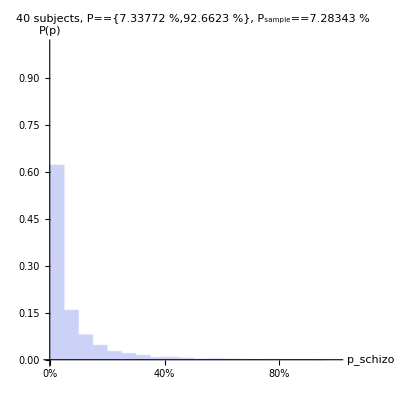

```mathematica
Table[histogram[jj],{jj,testnums}]
```

```mathematica
HistogramList[samples[20],{histbins},"Probability"]
```

{{{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1001/1000}},{{0.6209,0.1582,0.0798,0.0463,0.0269,0.0202,0.0142,0.0076,0.0079,0.0054,0.0025,0.0033,0.0024,0.0014,0.0006,0.0011,0.0008,0.0003,0.0002,0.}}}

```mathematica
samples[13][[1;;10]]
```

{{5.65887503258786×10^-1163},{1.30801867844547×10^-2488},{1.66124226714154×10^-1981},{4.07458410248596×10^-3257},{2.06631061136592×10^-2697},{5.012506343956×10^-1849},{5.36341149693812×10^-1548},{4.33348406457218×10^-1035},{4.83318403737227×10^-3678},{5.80100778372137×10^-1889}}

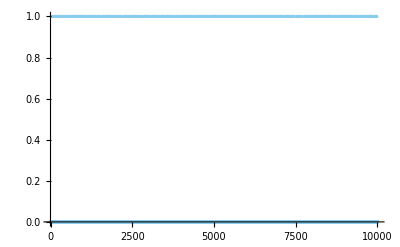

```mathematica
ListPlot[Flatten@samples[13],Joined->False]
```